# Take Home Final Report

## By Taylor Graham

## Problem 1

### Question 1:

The first thing I had to do was to simply plug in all of the data into Mathematica so that I had something useful to work with.  I did this by just copying line by line from 	the .txt file provided, and entered those lines into an array.  I then split that huge data array up into the different respectful variables, EX,ECAB,MET,GROW,YOUNG,OLD, and WEST.  The next task was to evaluate the different dependent variables compared against the dependent variable.  I originally did this by just plotting the data for a independent variable and the dependent variable on the same graph, but this turned out to be less useful than I anticipated.  Next was to plot the two different variables as a scatter plot, so you can easily see the correlation between variables.

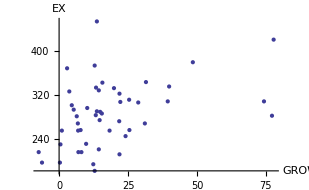
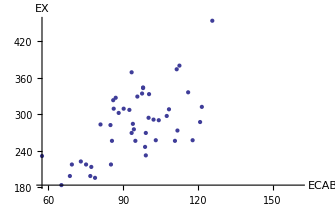

Out of all six plots, only two really appeared to have a linear correlation, and one was kind of a stretch at that.  I have included the plots of ECAB vs EX, which has the highest linear correlation, as well as GROW vs EX, which could possibly be considered constant, but I threw it in there to make it more interesting!

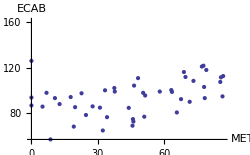
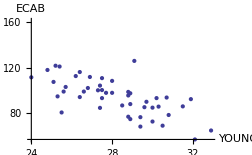
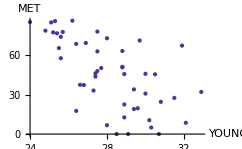
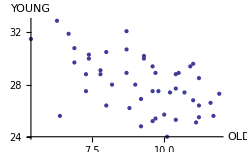

When evaluating the relationships between the dependent variables, I found that the YOUNG dataset causes the most colinearity overall, which I thought was interesting.  The graphs above highlight the most colinear variables, though the first two have a pretty small correlation.

### Question 2:

Next I was tasked with finding the regression model for this data, which involves finding the 6 different regression coefficients, as well as the intercept.  Luckily enough, Mathematica will do all of the hard work for me, I just had to set it up!  I had to modify how my data was formatted (put y at the end of each array instead of at the beginning).  Mathematica has this really nice built in function that will estimate linear models for you, given an input array and all of the variable names.  I used this method to come up with the lovely formula for the multiple regression model.

OverHat[EX]=356.182 + 1.4185 ECAB - 0.660153 MET + 0.57159 GROW - 6.67466 YOUNG - 1.85507 OLD + 35.4723 WEST

I' m surprised by the last parameter coefficient, for western states.  This means that western states can expect an average of $35.5 more per capita expendatures compared to eastern states.  I fully expected both ECAB and MET to have the biggest effect on the expendatures, But it seems like those two variables have a relitavely small effect on the final outcome.  Even the population age has a greater effect, where high amounts of either young or old people in a state can sort of stunt the expendature totals.

### Question 3:

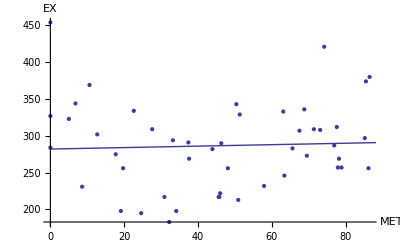
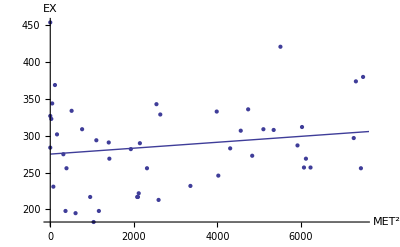
For part 3 I decided to add MET^2 to the regression model, so that it would hopefully account for the nonlinearity of the correlation between MET and EX.  Following is a scatter plot of MET^2 vs EX, and you can start to see a very small positive linear correlation between the two variables now. 
-Graphics-           -Graphics-

The regression equation is as follows

OverHat[EX]=119.118+1.39542 ECAB-3.04214 MET+0.695336 GROW+0.607602 YOUNG+4.12078 OLD+34.0731 WEST+0.030914 (MET^2)^

I would say that this model is less accurate compared to the original one that I came up with in part 2.  For one thing, the coefficient before MET is now negative, so having a larger population means lower expendatures, which is opposite from before.  The opposite observation can be made for the young and old variables; they now have a positive effect on expendatures, where it was negative before.  None of this stuff gets accounted for by the MET^2 variable, as its coefficient is a measly 0.03.

### Question 4:

Question 4 asks us to take the regression model from part 3, and remove any variables that have a large p-value, until none of the p-values are greater than 0.05.  I started with the regression model from part 2, because I feel that that was a better model for me to work with initially.  Mathematica has another nice function to evaluate the parameters p-values for a linear model, so I used that to determine which parameter had the highest p-value.  Initially, it was the WEST parameter that had the highest p-value, at .79, so I got rid of that value first!  Next I performed another linear analysis to get an updated model without the WEST parameter, and recalculated p-values on this new model.  Again there were large p-values, and I chose to eliminate the OLD parameter, as it had a p-value of .91.  I repeat this process a third time, this time eliminating the ECAB parameter with its p-value of .13, were getting close!  I performed a linear regression one more time, and reached my final model, as all parameters have p-values well under 0.05.

OverHat[EX]=668.821+1.52654 GROW-0.982591 MET-12.9968 YOUNG

Final p-values for {GROW, MET, YOUNG, EX}

{9.85785×10^-6,0.0117987,0.000824996,0.00486014}

The fact that all of the remaining p-values are well below 0.05 indicates that we can reject the null hypothesis.  This means that we can have confidence that the new model is better than the one calculated in question 3.

### Question 5:

## Problem 2

### Question 1: